编写优秀的代码

写好代码在很多方面就像写好散文一样：你需要有清晰的思路，并且能够很好地表达出来。当你刚开始写代码时，你很可能会用英语或任何你使用的自然语言来思考你的代码是做什么的。但当你熟练掌握 Wolfram 语言后，你就会开始直接用代码来思考，对你来说，打出一个程序比描述它的作用更快。

作为语言设计者，我的目标是使 Wolfram 语言的表达尽可能地简单。Wolfram 语言中的函数很像自然语言中的词汇，我一直在努力地选择好它们。

像 Table、NestList 或者 FoldList 这样的函数存在于 Wolfram 语言中，因为它们表达了人们想要做的普通事情。就像在自然语言中一样，原则上总是有很多方法可以表达一些东西。但好的代码需要找到最直接、最简单的方法。

要在 Wolfram 语言中创建前 10 个数字的平方的表，有一段显而易见的优秀代码，就是只使用函数 Table。

简单又优秀的 Wolfram 语言代码，用于创建前 10 个数字的平方的表：

```mathematica
Table[n^2,{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

为什么会有人写出其他东西呢？一个常见的问题是没有考虑“整个表”，而是考虑构建表的步骤。在早期计算阶段，计算机需要所有能得到的帮助，人们没有选择，只能给出描述每一步的代码。

一段更糟糕一些的代码，一步一步地建立表：

```mathematica
Module[{list,i}, list={}; For[i=1,i≤10,i++, list=Append[list,i^2]];list]
```

{1,4,9,16,25,36,49,64,81,100}

但 Wolfram 语言的意义在于让人们在更高的层次上表达事情，并创建尽可能直接捕捉到人们想要做的概念的代码。一旦了解了这门语言，在这个层次上的操作就会大大增加效率。而且，这样的代码对计算机和人类来说都更容易理解。

在编写优秀的代码时，重要的是要经常问：“这段代码要做什么的大背景是什么样的？” 通常情况下，你一开始会只理解其中的一部分，并且只为这一部分写代码。但是，你最终会扩展它，并在你的代码中加入越来越多的部分。但如果你考虑到整体，你可能会突然意识到有一些更强大的功能，比如  Fold，你可以用它来使你的代码重新变得漂亮和简单。

编写代码，将{百、十、个}位数转换为一个整数：

```mathematica
fromdigits[{h_,t_,o_}]:=100h+10t+o
```

运行代码：

```mathematica
fromdigits[{5,6,1}]
```

561

用 Table 来推广到任何长度的列表：

```mathematica
fromdigits[list_List]:=Total[Table[10^(Length[list]-i)*list[[i]],{i,Length[list]}]]
```

新的代码也能正常工作：

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

简化代码，让将整个 10 的幂指数列表同时进行相乘：

```mathematica
fromdigits[list_List]:=Total[10^Reverse[Range[Length[list]]-1]*list]
```

尝试另外一种不同的、递归的方法，首先清除之前的定义：

```mathematica
Clear[fromdigits]
```

```mathematica
fromdigits[{k_}]:=k
```

```mathematica
fromdigits[{digits___,k_}]:=10*fromdigits[{digits}]+k
```

新方法也能正常使用：

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

然后你意识到，其实这一切都只是 Fold！

```mathematica
Clear[fromdigits]
```

```mathematica
fromdigits[list_]:=Fold[10*#1+#2&,list]
```

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

当然，也有一个内置函数可以完成这个功能：

```mathematica
FromDigits[{5,6,1,7,8}]
```

56178

为什么代码简单是好事？首先，因为它更有可能是正确的。复杂的代码比简单的代码更容易隐藏错误。简单的代码通常也更通用，所以它甚至可以覆盖你没有想到的情况，避免你写更多的代码。最后，简单的代码往往更容易阅读和理解。(简单并不总是等同于短，事实上，短的“代码诗”会让人难以理解。)

一个过于简短的 fromdigits 版本，已经开始难以理解了：

```mathematica
fromdigits =Fold[{10,1}.{##}&,#]& ;
```

虽然它也能正常工作：

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

如果你想做的事情很复杂，那么你的代码可能不可避免地需要复杂化。不过，好的代码会被分解成函数和定义，每个函数和定义都尽可能的简单和自足。即使在非常大的 Wolfram 语言程序中，也可能没有超过几行的单独定义。

这里有一个结合几种情况的单一定义：

```mathematica
fib[n_]:=If[!IntegerQ[n]||n<1,"Error",If[n==1||n==2,1,fib[n-1]+fib[n-2]]]
```

把它分解成几个更简单的定义会好很多：

```mathematica
fib[1]=fib[2]=1;
```

```mathematica
fib[n_Integer]:=fib[n-1]+fib[n-2]
```

写好代码的一个非常重要的方面是为你的函数选择好的名字。对于 Wolfram 语言的内置函数，我在几十年的时间里做出了巨大的努力，来选择好的名字，以在其简短的名字中抓住函数的本质，以及如何考虑它们。

当你编写代码时，首先定义一个新的函数是很常见的，因为你需要它在某些非常具体的场景中使用。但是，起一个即使在这个场景外也能理解的名字几乎总是值得尝试。如果你找不到一个好的名字，这往往是一个迹象，表明它不是一个适合在此处定义的函数。

一个好的函数名称的标志是，当你在一段代码中读到它时，你会立即知道代码的作用。事实上，Wolfram 语言的一个重要特点是，直接阅读和理解写得很好的代码，通常比从任何类型的文本描述中阅读和理解更容易。

如何用通俗的英语描述这个呢？

```mathematica
Graphics[{White,Riffle[NestList[Scale[Rotate[#,0.1],0.9]&,Rectangle[ ],40],{Pink,Yellow}]}]
```

-Graphics-

当你编写 Wolfram 语言的代码时，你有时不得不在使用一个罕见的内置函数，但这个函数恰好可以做你想要的事情，与使用几个更常见的函数来创建相同的功能之间进行选择。在本书中，我有时会选择避免使用罕见的函数，以减少词汇量。但最好的代码倾向于在任何时候都使用单个函数，因为函数的名称可以解释代码的意图，而单独的代码段则不能。

使用一小段代码来反转一个整数数字：

```mathematica
FromDigits[Reverse[IntegerDigits[123456]]]
```

654321

使用单个内置函数可以更清楚地解释其意图：

```mathematica
IntegerReverse[123456]
```

654321

好的代码需要正确并易于理解。但也需要高效地运行。在 Wolfram 语言中，更简单的代码通常也是更好的，因为通过更清楚地解释你的意图，Wolfram 语言能更容易地优化你所需的内部计算。

随着每个新版本的推出，Wolfram 语言在自动找出如何使你的代码快速运行方面都做得更好。但是，你总是可以通过良好的算法结构来帮助你。

Timing 可以给出一个计算的时间(以秒为单位)及其结果：

```mathematica
Timing[fib[20]]
```

{0.021843,6765}

根据上面的定义，绘制出计算 fib[n] 的时间。

根据上面定义的 fib，时间增长得非常快：

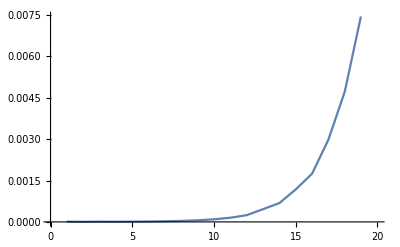

```mathematica
ListLinePlot[Table[First[Timing[fib[n]]],{n,20}]]
```

我们使用的算法恰好做了一个指数级的不必要的工作，重新计算它之前已经计算过的东西。我们可以通过定义使 fib[n_] 总是为 fib[n] 进行赋值来避免这个问题，它将存储每个中间计算的结果。

重新定义 fib 函数使之记住它计算的每一个值：

```mathematica
fib[1]=fib[2]=1;
```

```mathematica
fib[n_Integer]:=fib[n]=fib[n-1]+fib[n-2]
```

现在，即使到了 1000，每个新值也只需要微秒的时间来计算：

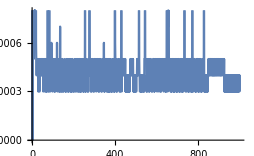

```mathematica
ListLinePlot[Table[First[Timing[fib[n]]],{n,1000}]]
```

词汇

FromDigits[list] |   | 根据各位数字来构建整数
IntegerReverse[n] |   | 反转整数的各位数字
Timing[expr] |   | 进行计算，并计时

"共有 5 道习题" | "开始练习 »"

找出 Module[{a,i},a=0; For[i=1,i≤1000,i++,a=i*(i+1)+a];a] 的更简单的形式。»

| 期望输出： |  
  | 334334000 |

找出 Module[{a,i},a=x; For[i=1,i≤10,i++, a=1/(1+a)];a] 的更简单的形式。»

| 期望输出： |  
  | 1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x)))))))))) |

找出 Module[{i,j,a},a={}; For[i=1,i≤10,i++,For[j=1,j≤10,j++,a=Join[a,{i,j}]]];a] 的更简单的形式。»

| 期望输出： |  
  | {1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,1,10,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9,2,10,3,1,3,2,3,3,3,4,3,5,3,6,3,7,3,8,3,9,3,10,4,1,4,2,4,3,4,4,4,5,4,6,4,7,4,8,4,9,4,10,5,1,5,2,5,3,5,4,5,5,5,6,5,7,5,8,5,9,5,10,6,1,6,2,6,3,6,4,6,5,6,6,6,7,6,8,6,9,6,10,7,1,7,2,7,3,7,4,7,5,7,6,7,7,7,8,7,9,7,10,8,1,8,2,8,3,8,4,8,5,8,6,8,7,8,8,8,9,8,10,9,1,9,2,9,3,9,4,9,5,9,6,9,7,9,8,9,9,9,10,10,1,10,2,10,3,10,4,10,5,10,6,10,7,10,8,10,9,10,10} |

创建一个计算 n^n 所需时间的线条图，其中 n 最大为 10000。»

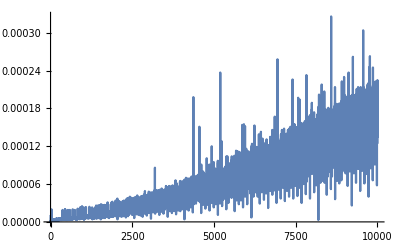
| 期望输出： |  
  | -Graphics- |

创建一个排列随机顺序的 Range[n] 所需时间的线条图，其中 n 最大为 200。»

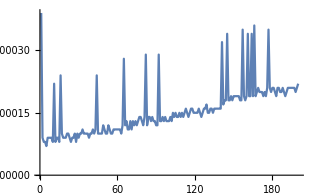
| 期望输出示例： |  
  | -Graphics- |

问&答

i++ 是什么意思？

这是对 i=i+1 的一个简化表述。这与 C 语言和许多其他低级计算机语言中进行这种增量操作的符号相同。

For 函数是做什么的？

它类似于 C 语言中的 for(...) 语句。For[start,test,step,body] 首先执行 start，然后检查 test，然后执行 step，然后执行 body。它反复进行这些操作，直到 test 不再给出 True。

为什么缩短的代码片断会让人难以理解？

最常见的问题是，变量，有时甚至是函数都被剔除了，所以可以读到的名字就更少了，而这些名字可能会提供关于代码应该做什么的线索。

编写 Wolfram 语言代码的最佳 IDE 是什么？

对于日常编程，Wolfram 笔记本就是最好的。请确保在你的代码旁边添加章节、文本和例子。对于大型的多开发者软件项目，Wolfram Workbench 提供了一个基于 Eclipse 的 IDE。

Timing 实际上测量的是什么？

它测量的是 Wolfram 语言计算你的结果实际所花费的 CPU 时间。它不包括显示结果的时间。它也不包括用于外部操作的时间，比如从云端获取数据。如果你想要绝对的完整时间，请使用 AbsoluteTiming。

如何才能为快速运行的代码获得更准确的计时？

使用 RepeatedTiming，它可以多次运行代码并对得到的时间进行平均。(如果代码会自己变化，比如上面 fib 的最后一个定义，这样就是无效的。)

有哪些加快代码速度的技巧？

除了保持代码简单外，还有一点就是不要重新计算任何不必要的东西。另外，如果你要处理大量的数字，使用 N 来强制使用近似数字可能会有帮助。对于一些内部算法，你可以选择你的性能目标(PerformanceGoal)，通常在速度和精度之间进行权衡。还有一些函数，比如 Compile，会强迫将更多与优化相关的工作在前面完成，而不是在计算过程中完成。

技术笔记

极其简单的代码也可以产生非常复杂的行为：这就是我 1280 页的书《A New Kind of Science》的内容。一个很好的例子是 CellularAutomaton[30,{{1},0}]。

fib 函数是计算 Fibonacci[n]。原来的定义总是顺着一整棵树向下递归 O(ϕ^n) 个值，其中 ϕ≈1.618 是黄金比例(GoldenRatio)。

记住一个函数之前计算过的值，有时被称为记忆，有时也称为动态编程，有时也称为缓存。

函数 IntegerReverse 在 10.3 版本中有更新。

对于大型程序，Wolfram 语言有一个框架，可以将函数隔离到上下文和包中。

If[#1>2,2#0[#1-#0[#1-2]],1]&/@Range[50] 是简短代码的一个示例，理解起来有点挑战性...